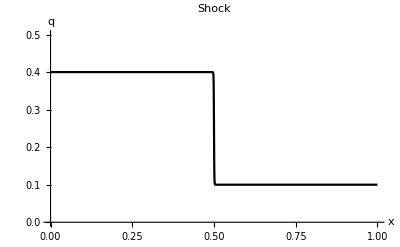

```mathematica
qleft = 0.3;
qright = 0.1;
discontinuity= 100;
h[x_]:=Piecewise[{{qleft, x<=0.5}, {qright, x>0.5}}]
Plot[0.15Tanh[-1000(x-0.5)]+.25,{x, 0,1},PlotRange->{0,0.5},PlotStyle->Black,PlotLabel->Style["Shock",Black],AxesLabel->{Style["x",Bold,Black],Style["q",Bold,Black]}]
```

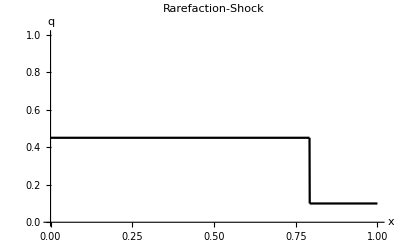

```mathematica
qleft = 0.45;
qright = 0.1;
s = (f[qleft]-f[qright])/(qleft-qright);
h[x_,t_]:=Piecewise[{{qleft, x≤s*t+0.5}, {qright, x>s*t+0.5}}]
Plot[h[x,1.0],{x,0,1.0},PlotRange->{0,1.0},PlotStyle->Black,PlotLabel->Style["Rarefaction-Shock",Black],AxesLabel->{Style["x",Bold,Black],Style["q",Bold,Black]},ExclusionsStyle->{Directive[Black,Thickness[0.004]]}]
```

```mathematica
s
```

0.2925

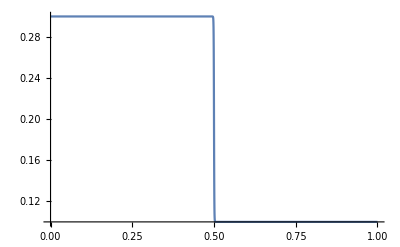

```mathematica
Plot[0.1Tanh[-1000(x-0.5)]+.2,{x,0,1}]
```

```mathematica
f[q_]:=(q^2-q^3)
g[q_,qright_,qleft_]:=(f[qleft]-f[qright])/(qleft - qright)*(q - qleft)+f[qleft]
(f[qleft] - f[qright])/(qleft - qright)
```

0.27

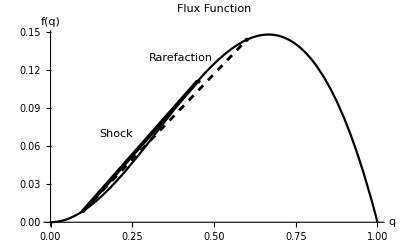

```mathematica
qleft=0.6;
qright = 0.1;
p=Plot[f[q],{q,0,1},PlotStyle->Black,PlotLabel->Style["Flux Function",Black],AxesLabel->{Style["q",Bold,Black],Style["f(q)",Bold,Black]}];
gr = Graphics[{Black,PointSize->Medium,Point[{{qright,f[qright]},{qleft,f[qleft]}}],Thickness[0.007],Line[{{qright,f[qright]},{qb,f[qb]}}],Dashed,Thickness[0.005],Line[{{qright,f[qright]},{qleft,f[qleft]}}],PointSize->Large,Point[{qb,f[qb]}],Text["Shock",{0.2,0.07}],Text["Rarefaction",{0.4,0.13}]}];
Show[p,gr]
```

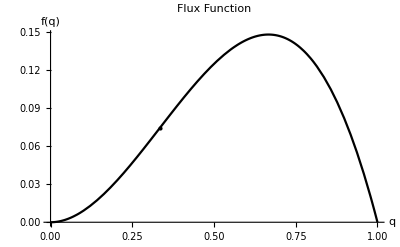

```mathematica
qleft=0.6;
qright = 0.1;
p=Plot[f[q],{q,0,1},PlotStyle->Black,PlotLabel->Style["Flux Function",Black],AxesLabel->{Style["q",Bold,Black],Style["f(q)",Bold,Black]}];
gr = Graphics[{Black,PointSize->Large,Point[{{1/3,f[1/3]}}]}];
Show[p,gr]
```

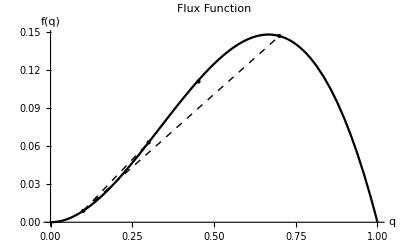

```mathematica
qleft1=0.3;
qleft2=0.7;
qright = 0.1;
qb = (1 - qright)/2;
p=Plot[f[q],{q,0,1},PlotStyle->Black,PlotLabel->Style["Flux Function",Black],AxesLabel->{Style["q",Bold,Black],Style["f(q)",Bold,Black]}];
gr = Graphics[{Black,PointSize->Medium,Point[{{qright,f[qright]},{qleft1,f[qleft1]},{qleft2,f[qleft2]}}],Dashed,Line[{{qright,f[qright]},{qleft1,f[qleft1]}}],Line[{{qright,f[qright]},{qleft2,f[qleft2]}}],PointSize->Large,Point[{qb,f[qb]}]}];
Show[p,gr]
```

```mathematica
qleft=0.6;
qright = 0.1;
p=Plot[f[q],{q,0,1},PlotStyle->Black,PlotLabel->Style["Flux Function",Black],AxesLabel->{Style["q",Bold,Black],Style["f(q)",Bold,Black]}];
gr = Graphics[{Black,PointSize->Large,Point[{{1/3,f[1/3]}}]}];
Show[p,gr]
```

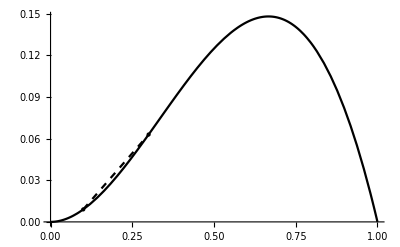

```mathematica
Show[,Epilog->{Black,PointSize@Large,Point[{{0.1,f[0.1]},{0.3,f[0.3]}}]}],Plot[g[q,0.1,0.3],{q,0.1,0.3},PlotStyle->{Black,Dashed}]]
```

```mathematica
??Point
```

RowBox[{"Point", "[", StyleBox["p", "TI"], "]"}] is a graphics and geometry primitive that represents a point at StyleBox["p", "TI"]. 
RowBox[{"Point", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a collection of points.

Attributes[Point]={Protected,ReadProtected}
 
Options[Point]={VertexColors→None,VertexNormals→None}

```mathematica
??Epilog
```

Epilog is an option for graphics functions that gives a list of graphics primitives to be rendered after the main part of the graphics is rendered.

Attributes[Epilog]={Protected}